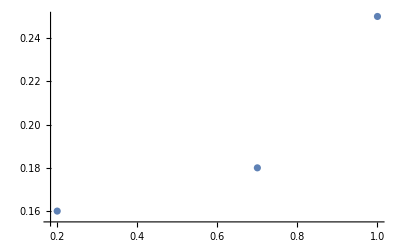

```mathematica
A={{1,0.25}, {0.20, 0.16}, {0.70,0.18}};
ListPlot[A]
```

```mathematica
approx=Fit[A,{1,x^3},x]
```

0.154823+0.0929161 x^3

```mathematica
0.08425257886878161+0.22301200443453742 x^3
```

0.0842526+0.223012 x^3

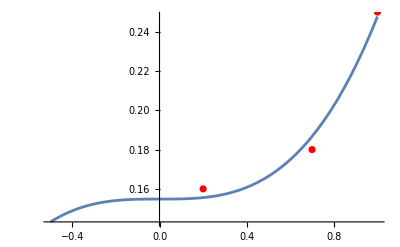

```mathematica
Show[Plot[approx,{x,-0.5,1}],ListPlot[A,PlotStyle->Red]]
```